## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Prepare Spectrum

```mathematica
dataFake={{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}
dataFake2={{-1,-1.3},{-0.8,-1.0},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}
```

{{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}

{{-1,-1.3},{-0.8,-1.},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}

```mathematica
spectFunCrossing[u_]=CoefficientList[
Fit[dataFake,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

2.50958+4.51014 u+12.6683 u^2+9.1079 u^3-11.5219 u^4-11.2738 u^5

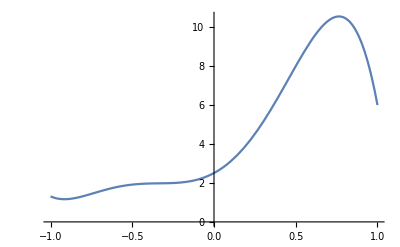

```mathematica
Plot[spectFunCrossing[u],{u,-1,1}]
```

```mathematica
spectFun[u_]=CoefficientList[
Fit[dataFake,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

2.50958+4.51014 u+12.6683 u^2+9.1079 u^3-11.5219 u^4-11.2738 u^5

```mathematica
Plot[spectFun[u],{u,-1,1}]
```

-Graphics-

I can try to find the three useful integrals analytically. It can be done but I will try to do this more generally.

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)/(1-n u),{u,-1,1}]
]
```

ConditionalExpression[1/n^6(n (22.5476+n (23.0437+n (-10.6999+(-17.6554-10.5827 n) n)))+(11.2738+n (11.5219+n (-9.1079+n (-12.6683+(-4.51014-2.50958 n) n)))) Log[1.-1. n]+(-11.2738+n (-11.5219+n (9.1079+n (12.6683+n (4.51014+2.50958 n))))) Log[1.+1. n]),-1.<n<1.]

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)u/(1-n u),{u,-1,1}]
]
```

$Aborted

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)u^2/(1-n u),{u,-1,1}]
]
```

ConditionalExpression[1/n^8(n (22.5476+n (23.0437+n (-10.6999+n (-17.6554+n (-10.5827+(-8.85595-3.42884 n) n)))))+(11.2738+n (11.5219+n (-9.1079+n (-12.6683+(-4.51014-2.50958 n) n)))) Log[1.-1. n]+(-11.2738+n (-11.5219+n (9.1079+n (12.6683+n (4.51014+2.50958 n))))) Log[1.+1. n]),-1.<n<1.]

Define a test spectrum function which is identity.

```mathematica
spectFun2[u_]:=1
```

Define the three integrals

```mathematica
IntFun0nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun1nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)u/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun2nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)u^2/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun0nFF[0.1,1,-1,spectFun]
IntFun2nFF[0.1,1,-1,spectFun]
IntFun2nFF[1.1,1,1/1.1+0.00001,spectFun]
IntFun2nFF[1.1,1/1.1-0.00001,-1,spectFun]
```

-9.23544

-3.66056

61.2581

-69.4532

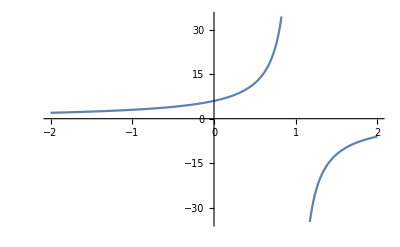

```mathematica
Plot[(spectFun@u)/(1-n u)/.u->1,{n,-2,2},Exclusions->{1}]
```

```mathematica
SpectrumOmegaNMAATest[n_?NumberQ,ct1_,ct2_,spectrumFun_]:=(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun])/(-4)
```

```mathematica
SpectrumOmegaNMZATest[n_?NumberQ,ct1_,ct2_,spectrumFun_]:=-{(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun]+√((IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]-2IntFun1nFF[n,ct1,ct2,spectrumFun])(IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]+2IntFun1nFF[n,ct1,ct2,spectrumFun])))/(-4),
(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun]-√((IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]-2IntFun1nFF[n,ct1,ct2,spectrumFun])(IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]+2IntFun1nFF[n,ct1,ct2,spectrumFun])))/(-4)
}
```

```mathematica
SpectrumOmegaNMAA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.9,1,-1,spectFun]
SpectrumOmegaNMZA[0.999,1,-1,spectFun]
SpectrumOmegaNMZA[0.9999,1,-1,spectFun]
```

1.39372

{1.21279,-4.00023}

{2.11188,-6.92597}

{4.72858,-10.8294}

{5.8447,-11.9815}

```mathematica
SpectrumOmegaNMAATest[0.3,1,-1,spectFun]
```

1/4 (-IntFun0nFF[0.3,1,-1,spectFun]+IntFun2nFF[0.3,1,-1,spectFun])

```mathematica
SpectrumOmegaNMAATest[-0.999,1,-1,spectFun]
SpectrumOmegaNMAATest[-0.99999,1,-1,spectFun]
SpectrumOmegaNMAATest[-0.999999999999,1,-1,spectFun]
```

1.35328

1.35671

1.35678

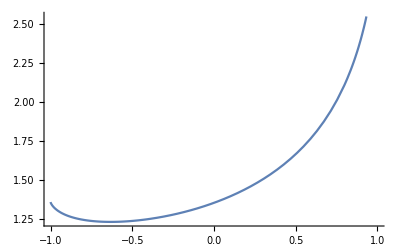

```mathematica
Plot[
SpectrumOmegaNMAATest[n,1,-1,spectFun],
{n,-1,1}
]
```

```mathematica
Plot[
SpectrumOmegaNMZATest[n,1,-1,spectFun2][[1]],
{n,-0.99,0.99}
]
```

Cell[BoxData[
 GraphicsBox[{{}, {}, 
   {RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6], Opacity[
    1.], LineBox[CompressedData["
1:eJwt2Xk0lF8fAHAhSbInFZXsUdm16atCSCUiISGkspNs2UISChGyp8jSYldy
oyJromcwzDDD2MZMC1qp9/7Oef+a8/ljnnvuvc93O4+0k5e5CycHB0fmCg6O
/37rtgwcNMtjI9dmEfUREgNkrjVZh99jI2fBV1yfXjCAb5eLepUXGwXVPIrq
02HA9h9hSccvsVF1gZe8rAIDTFDG7IwzGxm1rRh/Ls6Amye6CrfasFEHsRwS
8n0CeL01RJP02WhhaU4lr34CVj5fseC2gY04Qq5uETacANmgTWbcYmyk6Nkt
FLt7AvQPapXnCbDRaoPuLzLKExD90c2ZxMVG5ba2yyShCeD89uHTYTYL8TO7
Tbmo48ChkVuz+Q0LLazQKe0NG4etf+qEX7xioZI08ahAv3HQe/PRw7KehRTF
Un/puo1DuMVK+YQKFnpy+N79Lebj8NfPPf3XPRbaVmpnuEthHP5U7736yZ2F
VG3Wdq4n0eG79sDueHEWktXclWilT4eocWHRSGEWmjyY8M59Px0E7piyrvKz
kKl8vUGKJh0UZpoLXDhZqD3F1ZRPjg7W98v5DrLnUEGX2EIJDx0a/kWO/Hg3
h26d0mi52kWD0PcqES5X5lCYICfPAUca8F65YGPnPYfSr8efnLahwV3pQk2L
y3PIW445k32KBhXB62f0HOeQdZh8gqwRDagqnOaSx+aQ5LOAa6W7aKCXPCDT
LzuHtPYpNwZx0IDLJqpN7xMTvX7cfyi8ZAxks/yZZh+YSETreJTdgzHQJ7sK
OnYwUbzX3RG93DGItjl6OvI1E73UQzmb744Bt63YVHM5E1WbL0erRIwBj90j
nsMxTETwKKpGnxkDXvsOAwNtJhK/KeWPhMZAMbfxoqUaE1E8NTae5x8DI+qT
RBcVJqJK1Uny845BnH0qEbONif4UXRAb+TsKq8/ZubQKMFFR0rHHYyOjwOfA
jj4yNYs4eTyXO7JGYa2TyFvjjFl02M+BlCM1CkJ3Z96zU2aRaf79477rRkG0
9XV3auIsEhE5m222dhQ2bPcaoETNIqfCDRe3L1NB7lvnrI/HLJLTaSoxo1BB
NypGOOvQLMpquhpxOo8KHoU/7WfnZhBHogqLpESFbjr1V/zBGZRLRbKXLSmw
/xcp9Nb+GWScQdzIP0GBcsEP/27pzKBET50zw8YUSNiPVibumEHft/bIOR6g
gEl6nvDtDTPI/O7HqHIFCrQaOyilfp1Gbos3Lu37MwJNz2jW9wum0cZNIwY8
j0bgSdhEXdmKafRM5+8BOu8IcNxo3nRwaQqZrQuPHuQaAYvbueGk71Molv3B
oP/vMPzMsz6yYm4KeUcR20gLw3CwuYtkRZpCAtrMTCHaMHziqllcUTaF3IUr
9SxeDMPvuBgN61NTiF/09+KU1zAYpso/5S6eROfMHUY1J8mgsuulXVXBJGL8
QV3qdDKIdJ7gc8qeRBxuI0MaVDKMcga5oORJ1J2frw8kMgT6dm4KDp1EVjwC
P4JbyVB20jvu88lJ1EMOaYgqJoOQ0AtH8hIDaRz9pNN4mQzDCcfEnpkzUGVV
VbjK0hAkF1Ss2LduAnVfItOe6Q/B8k4Txb+NdKS59tmazPuDED+wZSA/hIac
d9RrXxMbBDEX8nya3hgyV3u/p65gAB6TClNjCQrS0C+oZWkNgPsGLrP808PI
43hLF5VKgvvHRsK2Fw0i9lvS2ZOJJGg9Gn7zzDKBem+uras2IoFaxN2iI9H9
6CgvSZoqTIL39R2bE4P60Yf9St6c2A5fOTL7PPuRR4KKpYIQCZKcPBLPnulH
heBE9xUgwZy+YYDfzn4kSXPnEl5DgpLVP4/kDfYh3qCWXRe5SbA51Zb5XaUP
BfoJv7jxgwC+R9vUHxG9yPglK8R3lIDg4qySws5e9DtTV6SNSgCzRGRLXnMv
snFibJXE7irj5M+o6EVOnuWP2kYISHxOZ9yM6UV+HTvMZMkECL0qzPTQ6kXb
rEWW5j8RsLPEgPPS9g9IXjOhldlBgBG3Yf6Nx13o46Y93Nr1BFT3tAt9Su1C
ZEps2/06ArZmHovcGtaF1BMeCHBi/9ph6dRg3oUMz9Ur9NYQUHraWZb5pxOV
/7aP9K0iYE1ZVMnx451Iuyy16sMTAnpOomfr5tuR79CbbcyHBOyVPCztRGlH
fGRjSUfsR5OtyU/a2pFwrE3aQBEB4SE9vkey21F6bfbK1gcEqD6kaAYZtCO5
WbXhkgICUn7+qR+59x4xf4ZAbA4Blnm7mx/sb0OlYec35qURIFKfZW2p0Iau
H1fhUsDu6V36zCPShhI/nDj/9C4BhpzNmy9NteL6cOBmcyoB2i7GoaoprUjy
7IQbM5kAcWUbnVdT75D6tjWOlkkEkGpDKkgpb9GZpMC4yBt4/Q8U/bhrb1H8
uy0qEtjHp2Fkj9tbROJbp/80loDWDdxrcnTfIqLwdi81hoDa0AS389Nv0CGL
U2cORxNw71COzBfdN+hExRfxbZEEWPc0Za6eaUb0wzVPtELw/wOLlJSIZqT0
p7l9LJgATZn4BqPmZuRu1XIkAVso0HLoRmYzin55zn0iiIB26TkJHpNmxD91
1iozEJ/vlQ0ZnGWv0ZusHfnrAvD+dk+r/BhqQn3ZRg9P++DzSawy1a5sQh+V
xTkFsdm0MPcr8U3odwHf61ZvfB+31pXP721C9Gca53Sw148eUv5y/xWq9d2o
JOVFwM+YHKWZs41IrENi7Lc7AS/7zeWHaQ1oISMz5q8bAU/qDI411zagFobP
UCN2/v3d/sW3GtDcgfqcEOzY85tb/LQa0Gva6au/LxBgPj9zlv9mPWqbdfFY
diVgViQyTVe1Dv12lD8j4UIA5btfo8zKOhRQlFVBcSagl+w6vppciz5Zl/k8
wK4tNFUjXa9FnGt9jFSxo9Qluj0HalD08327TpwnYKP5U+78sGrUxJs0UOBI
wFrtQuVYi2r0Ln7/Vk9sjo1p5u6K1WjsVM/AXuxJWnD+7r4q1NHinUo4EFDp
Y7j/o1wVCja9uU8I2ySZ4sfZ/Rw9ur3BMMuegPn89a3t2k9QWq845wo7Agqf
rvl+bLICrThK3KXYEmDW9E+uL60CFXTsufECu3x4Koa8UI4SLg/HX8F2Fq83
YFaWIX6Bfv4vNgQQt6zf8e96jHZ72H3/foaA6CzTxTvUElT+oShiCFv9sZ7c
uqQSRA7UutSIndSqGCPFKkaxaRttr2Mbrvilv7PsEbKIdq5ah10XkPn2hEIR
cn1XvcfUmgDXmMSFftIDpBi5s1YTW+xupKx17APkrVeULIXt/fxitAOjEIVK
+Ll8OU2A4twefZ8HBUh1646ILGzS7x3+i+YF6Kz3uoUY7OjV24qCOAtQvAy5
1Qd7TJ6PO8oxH41sn40zwVZ/U31DDnLRy/aWMA7spLHsqR25OajhnfIM2wrf
93L0Ee3lbBT6ybKSgv1gt+WqIy/vI6X2MYdGbLEni7FuOpkoXil8Zxi2dydl
0js9A+WczUnywu6afmcYtHgPdeW7HHPEjpFJ54mvSkfPJGYnDbC/Z2jHlu26
i2jMsJui2B8VhaUoyamoMvGCBC92eT2zSmAhBQWQ9nAuWxLgNJhP86lPRu4v
UiensHXdQgIfbExG38vW0yjYEj8tBYnQO0jo6zXtT9hZu8SDvaOSkHvv7Ndm
bLMTncX9honIDNinG7B5vCII7TUJSKSsW+I5tu+TWdXl1JtoY+/GsgJsxZ48
ewfrOLR3JCY0C5vKOpXwRvIG+h3fVpKKbbwDTd18GI1CZTqEb2D/NfVfx7p4
HelT445HYle7Kx022xmFHlE2TIZgX0qgeld9i0C31EIHA7D1rBV0d3iGo9xf
T+R8scvvJWfMfw9F+i7Puz3+28/An/mG8GBUUhXVexE7Wtz1RARvIKrV2LbT
FfuzZW+pYfIVJK5/e9IJ2yZtL8/ajX5I3aL91zns1k9Fjv2F3khz9MOFs9jO
ipuDNU67I+6AQlVb7H3F31Rfu11A+jV6p85gi8i3TZkGOyFHk9K+09j9xjq6
VettUdg3apkVdtSRsdKuvSdRYDB11BL7tZicU8ZVXbTQVOL5n/lnPHq4fsqA
abmu9X+eDDOW6KkzgqIDOdn/+W1zSG73bivojWzb99/z1jhdlCDzOYBXcqPW
f+tpjt91PPbLGQYzQuOtse2cX5e+nroIG/tX7bXBjmEw5zVIniB4y17fDvt0
1a1cC7oPmGyKfGyPPecnfTjxjD+Is70uOmJHaNZNtfYGQMI15WhnbLFF0wQO
oyDwt6j+dQG7pIauuheFgNPqNR2XsfcHBBJ+2mHwwEh10QvbbdOqVySrCNDv
kA3xx14eznYU6omC8rawe2HYRo1TGhWro+EU9+SOaOyUbHUeE4MY2LZy65Z4
bPmz70uvN94AoyghkXvY3rqi17b+jINU3XbRXOwXUvYnXmnEA3vvGe+H2Mep
8/PfSxNARYF7bw12RtOB1tTJRNjWL138Cns892aG6rbbYL9P0qsVu/Hp7c01
XXfAxq1CcOi/99tb7g37cCpENnmlcuL42VhULij9ORWKfG71CmBPDGjYWWTd
hSX74sBN2IFwaLHuSxrYWc6u1sbOEzinEJmTAUNXZ1W9sd0OTfpVGWXC1u2W
reHY6gEerxnzmVC5faD1NnYrJeSMicl98Dq4c/VzbHZ5xi3RHzlQ2HQz9Sd2
/diWQYPCXGAfEoxag/NLpFixbOCxPLB79H54MzZfE9mefTIfFhYmew2xc+Vm
fpiXFEA106DlPnbrwsrtkpZFkB5y9d0ZnP/KkozNakqLIFjM8KIf9h3FxIDj
HA8hQTslMBHbxk7sTUTZQ4i+UT/Ugs1+s82OsaIYZs0GH6njfCueCklPnjwG
B5UYH3mcz/+oXK8+wl0KWmWUD4bYY62t5LEzpfAjSTTrAnbp72MKoivLQD5e
3bcU+4CT3eurtuUgaftPTQvXBxe1oG96vE/hw/2d3+1xfYmKfqK9zfoptL48
dOU6du7AeDBXyVM4UVxuXoI9d6B4xbjMM/A8n604jy3PEI5/+OYZWLwrOZh4
loBMtams7VyVsD01Y2c/rl+Kwyt0NylXQru/Ufoydm205Ogai0o4v+K1neI5
AvoGTsqwCivBf16WJxybP6yx7OmhKhhcLOhUxfUwvCO5UTOqGt59DFd8hOun
gH+5vVxpNdj/vBxBws6WauMQ76sGPqkHOquc8H15L+n/kK6Bhtx1by9ifxO/
0N3QXAOFEjxWGrheu5zfTz2wog4qV8u6DuJ6fnRp8p9RRAN+/0NCLuH+oUWc
nJVS1gARKQu0Muy9at1aIyRs3b4GFvZ216rLXjteQPqpb698LxLA2xs+kEZ+
AVGcVhuiLuH88EDiKV2zER5LXFeqxf3LgaMm9qEzTRBtGLrJH/dDtS66v96J
Iag9Wtn5BntnhOpdQT0EKXN6n0V9CZCqEe8oTEcQ4lFxpwY77PbXrAnp1/Br
99MDf/1wPvn1imfNh9dw5wb/6Ye4/5LotqKeVmqBDg3/JZNQArj5v0XfO9AC
KRVDkcXYX0wSlQcsWiBfvzqQ+xoB79+/CbQKawGy9/qXCDvwraqoZX8L1K1t
ubsvnICBl3xG5tfeQOE1xwqjKALSS5uem358Cz/9BFc1xBGwLk4+5mBQG8Qa
uJr9SMfxrnVAQzSxDXba3Klwu0dAHN2SNpHfBlJfPXzJ2Ev7Y3Tj3rfBTdks
DZSB4/fr+GLP+vewW3RDemIWri+2Ba52te8htk/ws24u7td2SRpdnW8HlTX3
77Bw/36HJLymwqMLzFu9qIm1+Dwb07SUr3cB5/fsBjk8L7AKNjg8zuiC2V0/
1zVhm3hI1zx80wVXLFvNv+B5g5tb7Vzuhm4o9CkZs3mJ96tmVnX7XTccT9Ty
MHpNgGNCkq2v1AeYsq87HovnlQ0FK0n3J3thSdODkjaGz7dz5ecHX3rhs9kL
8iEajr/Flbzlv3thatWpk1+wRYx59jYKfISgfxxlpuM4H3zlyR3R/gi1weZi
aybx/vV4XaVufATvTT2juUwcn2N833MV+uD2D+GLMngeK9kqJF7o1g/y0qNq
jwVJoEsyC+bCc9dk6pV7HQYkcM6ScF+IG4Sha+cbbeNJcFTR85g8zzC0K1x7
mvmJBG/fmjRO1VNga/HH6Wa1AQhLs1m7uHkM+miao47pA5AzXtojY0uDxqFI
GcaqQVjZ0GS1sZIOYha1V56mD8Ixv0wrtW/jQGO6dSqrD8GpuaqP2T/GwYq1
l8KlNQQ2Lj2mvMvj4PmBoFB0hsD1NNfh0VUTkMx7r/Ke7hBE7PPYlSg1AX6T
KpRtxkNQyXWQd8ZoAuR7fUkZDkMgfne6IT9vAvieqU4LJQ8BtVpHSugYA5Sb
fKeKfw6BWVbWcSdzBiQ76HT8+TMELeHL4dWnGRD92kDQ/N8QFJu8oVs7MYBL
QKZjJQ8ZvMeOlxRcZcBqly9G8aJk4OJ31dAoZMBUmFvJ6l1kUDx/19jqBwPu
HhGoW7hABl/hr1eyCybhBjvvjjSdDIEiGkqpjybB9UPbrlEGGcJEr4zcLJuE
eMbz+LwZMtxc9+vQ1ZpJkL8+F674lQz5G1YImbdPgrPywitbjmH4IC1cuurr
JLyjrzE22TIMKupqVF+9KThWM4Lszw0Dw9zH0Hh0CppuyVupzwwDr1OPRNnE
FJhGp5+SZA/Ddh9lJv/sFNRY1T/kmx8G79uM270LU1DcJWa9sDQMS51nhk7z
TUPcx3/FS0IjIGZwyN1VaxqeyRhdmdwzAvo6oinXb00DWXFTzrHbI3DB0NuZ
cWcajtjY3+65OwLxlt3aR9KnISTm0ZNTWSPQ63djmK9gGk6pZ6d6PxwBu2d/
ZFNqp8Ewwoo09XIE/JQm6vJp0xDoOe8/PDMChZtqKK90ZmCdz4OPYiYUsDb8
qvZ2/wzUOohvpZ+ggKDPjtiOgzNwslNyrtqSAqGtD3cOHJ0BszULmy87UsDK
Jz38y7kZuEPcoG8MosDqtqvSMnEzoEkSfXH7MQW8ffe6xA3OQLm8wYKwIBXk
cwIakigz0PHvNk/BOipQ2irXptFn4NE0vVdbkgomUsq1BXMzIPA54mWAEhVk
329a9ZJjFgrrJFWN9akwILVcwlKchZ53XtqHQ6hwoB3NmQfNwsOu4KApNhUc
HPR/QNgsKLSbntT7ToXrP96v2HF9FvwpW/cVLFPhvVyf+KrEWZDtGIwI4R8F
86gJvZf5s6AYQYtM3T4KrvtWp8m8n4Uks2mLc26jkFRhrrsgzoSsC9Kdo7Oj
8Ex/4AhtExNszKysbedHoX/Y1rxnKxNCWwbUaX9GQYLP5ULJdibkz06JxPKM
QaHr1WS7A0yoem9Z+2X9GNRuyWa8dWFCsZT6QM++MaAkMxLTqplw6eKM0aq4
MZDUialjNTABPPLWeCaOgd2ILM0AMcF/zrZ7JGUMRuSdNb+3M6HFqSy/L2cM
yC/pZKtRJtzJjxmWrh6DAcaoggTfHNSXfXZ0oo/Bxz3k5qxzc1A4ElwmZUgD
odEg5jfnOVDsPaJWZUoDs+gN645emgPNskGeUxY06O2xdvvjPwcGronK9Q40
6Dk/IGAXPwdTQxyGAqE06Ez8ZCtVMwedkvlGojU0eEfrWczjY4G3xcW/NWp0
yCg8VpAtyIIUga7Aq3vo4H6+yzRTjAWFTvIjRw7SQYTR/iBlMwsUOTx2iJ+k
g/3025Mx6izwPNY37ulDhx/sFxWXbFjwY/P55sM1dOh4uufMhXMseB94JUKg
iQ653vXczs4s+B0c+5XZSgf9bzW2Zz1ZsPbwZf6xQTrcWXy22iyKBdodDQE1
y3RQWnrkolXKAk0e36azR8dhqVFOWP0pCyQWMn2DLMeh91pR485qFtz6ra5X
cW4cAv4ViCo2saDo8ulee/9xaOHMad7Yx4KWWeXlxdxxsF2dKsXxmwWxXn7J
Dr/GYWeHcPvSXxYc73P4qrVyAjhv3fH/xcWGlUE+UcrCE1DCn9T5bS0b5FQe
tgYpTcCC4M0ghjQbWtB2Uo3tBCSKhxMdxmwwHlJosWqbgMrBV39sT7DBNele
r+rABAxmLUmzTrHhwtkzuw9PTcC2LcGegg5sWBQu4l7Py4BahSurTgWwYXTR
NqXYlAHDM1U7GCFsOHhAXcTHngEc5d8sAiLZ8Eq1JyzCmwEmqt75GQlseJ0c
dzoojQEvnTbvtcvD6/3/+8v/AHGpKlo=
     "]]}},
  AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],
  Axes->{True, True},
  AxesLabel->{None, None},
  AxesOrigin->{0, 0.32},
  DisplayFunction->Identity,
  Frame->{{False, False}, {False, False}},
  FrameLabel->{{None, None}, {None, None}},
  FrameTicks->{{Automatic, Automatic}, {Automatic, Automatic}},
  GridLines->{None, None},
  GridLinesStyle->Directive[
    GrayLevel[0.5, 0.4]],
  Method->{"DefaultBoundaryStyle" -> Automatic, "ScalingFunctions" -> None},
  PlotRange->{{-0.99, 0.99}, {0.3333333360412254, 0.6824780443185261}},
  PlotRangeClipping->True,
  PlotRangePadding->{{
     Scaled[0.02], 
     Scaled[0.02]}, {
     Scaled[0.05], 
     Scaled[0.05]}},
  Ticks->{Automatic, Automatic}]], "Output",
 CellChangeTimes->{3.702246487472465*^9, 
  3.703334931488181*^9},ImageCache->GraphicsData["CompressedBitmap", "\<\
eJz

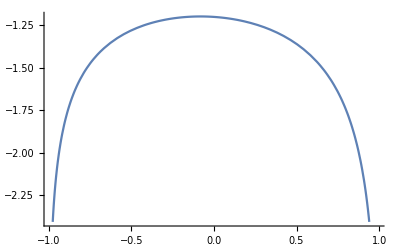

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[1]],
{n,-0.99,0.99}
]
```

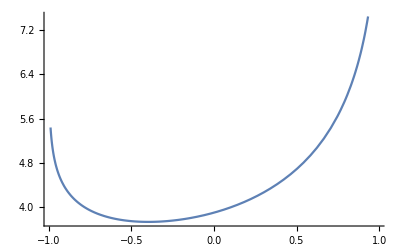

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[2]],
{n,-0.99,0.99}
]
```

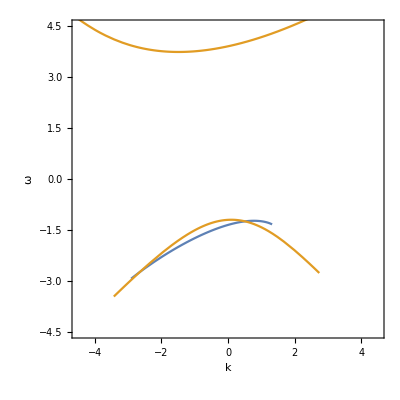

```mathematica
pltSpect=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,1,-1,spectFun],SpectrumOmegaNMAA[n,1,-1,spectFun]},
{n *#,#}&/@SpectrumOmegaNMZA[n,1,-1,spectFun]
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

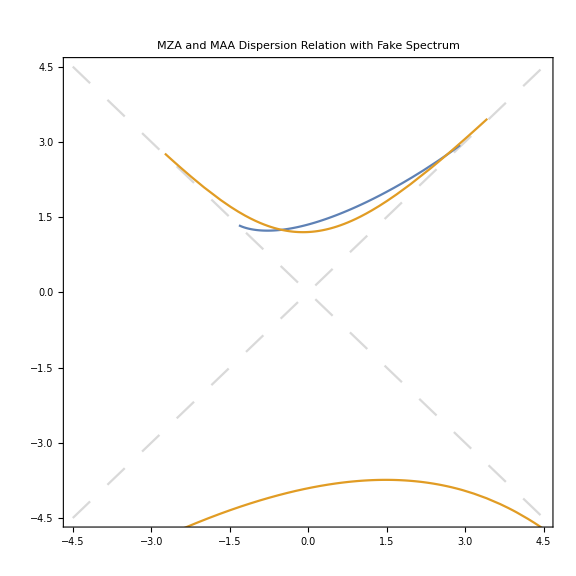

```mathematica
pltSpectGrids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpect
]
```

Linear Stability Analysis

I need to find the unstable values.

### Solve MAA

```mathematica
SpectrumOmegaNMAA[0.3,1,-1,spectFun]
```

1.5035

```mathematica
SpectrumOmegaKMAAEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM)/(-4);


{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
SpectrumOmegaKMAAEqnLHS[0.4,0,0.3,0,spectFun]
```

{2.40589,0}

Test FindRoot on this problem

```mathematica
FindRoot[
SpectrumOmegaKMAAEqnLHS[0.4,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
```

{kreal→-107.477,kimag→-2.78188×10^-24}

I need to generate all the results for different real omegas

```mathematica
maalsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMAAEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-0.91,0.91,0.1}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-0.0000310833}. NIntegrate obtained 0.0574177  - 0.00971492\ ⅈ and 7.99263×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.91,{0.99985,1.11213}},{-0.81,{1.06755,1.26625}},{-0.71,{1.13681,1.39729}},{-0.61,{1.20884,1.51032}},{-0.51,{1.28496,1.60857}},{-0.41,{1.36661,1.69449}},{-0.31,{1.45532,1.77035}},{-0.21,{1.55257,1.83863}},{-0.11,{1.65947,1.90231}},{-0.01,{1.77627,1.96472}},{0.09,{4.01402,-8.93432×10^-18}},{0.19,{6114.29,1.47512×10^-24}},{0.29,{-9331.45,-4.40807×10^-17}},{0.39,{12548.6,8.65899×10^-20}},{0.49,{543.912,-3.52704×10^-21}},{0.59,{-3220.55,8.05514×10^-26}},{0.69,{22200.1,3.31444×10^-26}},{0.79,{25417.3,2.37077×10^-28}},{0.89,{28634.4,9.14921×10^-27}}}

```mathematica
Export["maalsadata.csv",Flatten@#&/@maalsadata]
```

maalsadata.csv

### Solve MZA

```mathematica
SpectrumOmegaKMZApEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun1nFFM=NIntegrate[(spectM@u)u/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM+√((IntFun0nFFM+IntFun2nFFM-2IntFun1nFFM)(IntFun0nFFM+IntFun2nFFM+2IntFun1nFFM)))/(-4);



{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
SpectrumOmegaKMZAmEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun1nFFM=NIntegrate[(spectM@u)u/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM-√((IntFun0nFFM+IntFun2nFFM-2IntFun1nFFM)(IntFun0nFFM+IntFun2nFFM+2IntFun1nFFM)))/(-4);



{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
FindRoot[
SpectrumOmegaKMZApEqnLHS[0.3,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
```

{kreal→-6.14831,kimag→-0.0152747}

```mathematica
FindRoot[
SpectrumOmegaKMZAmEqnLHS[0.3,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]//Quiet
```

{kreal→-209.741,kimag→-0.0319845}

```mathematica
mzaplsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMZApEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-4.491,4.491,0.5}
]//Quiet
```

{{-4.491,{-1.87435,-6.31089×10^-30}},{-3.991,{-0.364055,-3.13777×10^-26}},{-3.491,{1.60332,1.70751}},{-2.991,{1.8415,2.93876}},{-2.491,{2.08266,3.75327}},{-1.991,{2.33021,4.37731}},{-1.491,{2.59125,4.87178}},{-0.991,{2.87742,5.26145}},{-0.491,{3.20731,5.55987}},{0.009,{9.64253,4.64449}},{0.509,{-3141.52,-0.0937844}},{1.009,{-283732.,3.36774×10^-7}},{1.509,{-1751.42,0.0000306366}},{2.009,{-426878.,-0.0000112193}},{2.509,{-326157.,429660.}},{3.009,{-442116.,0.000111045}},{3.509,{-47542.4,0.379289}},{4.009,{47643.7,-24791.9}}}

```mathematica
Export["mzaplsadata.csv",Flatten@#&/@mzaplsadata]
```

mzaplsadata.csv

```mathematica
mzamlsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMZAmEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-4.491,4.491,0.5}
]//Quiet
```

{{-4.491,{95.2511,-1.46433×10^-8}},{-3.991,{95.5903,-5.42315×10^-11}},{-3.491,{69599.1,-0.0163735}},{-2.991,{61155.7,-0.00152951}},{-2.491,{9974.9,0.00244043}},{-1.991,{1239.94,0.0377071}},{-1.491,{261262.,-8.46935×10^-9}},{-0.991,{-14220.3,176316.}},{-0.491,{-7014.36,41106.6}},{0.009,{-0.0266733,1.83325}},{0.509,{-0.0979696,1.48075}},{1.009,{-0.103901,0.814719}},{1.509,{0.998335,-3.96403×10^-29}},{2.009,{1.76647,-8.27515×10^-28}},{2.509,{2.38374,-3.80146×10^-23}},{3.009,{2.94442,-2.12644×10^-16}},{3.509,{3.47677,-5.54715×10^-20}},{4.009,{3.99369,-5.34643×10^-24}}}

```mathematica
Export["mzamlsadata.csv",Flatten@#&/@mzamlsadata]
```

mzamlsadata.csv

### Generate Map

```mathematica
maalsadata=Import["maalsadata-supernova.csv"];
mzaplsadata=Import["mzaplsadata-supernova.csv"];
mzamlsadata=Import["mzamlsadata-supernova.csv"];
```

Import::nffil: File not found during Import.

```mathematica
Flatten@#&/@maalsadata
```

$Failed

```mathematica
maalsadataClean=Select[Flatten@#&/@maalsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzaplsadataClean=Select[Flatten@#&/@mzaplsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzamlsadataClean=Select[Flatten@#&/@mzamlsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
```

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, -4.5 < #1 ⟦ 1 ⟧ < 4.5 && -4.5 < #1 ⟦ 2 ⟧ < 4.5 && -500 < #1 ⟦ 3 ⟧ < 500 &].

```mathematica
Dimensions@maalsadataClean
```

{4256,3}

```mathematica
mzamlsadataClean
mzaplsadataClean
```

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@maalsadataClean//Quiet
```

$Aborted

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@{Last@maalsadataClean}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.441553 - 1.2808×10^-16\ ⅈ and 0.278924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.0815534 - 2.56311×10^-19\ ⅈ and 0.00014022 for the integral and error estimates.

{{3.15026×10^-15,-3.19559×10^-17}}

```mathematica
Part[maalsadataClean,
Flatten@Position[
Chop[
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@maalsadataClean),
10^(-5)
]//Quiet,
{0,0}]
];
```

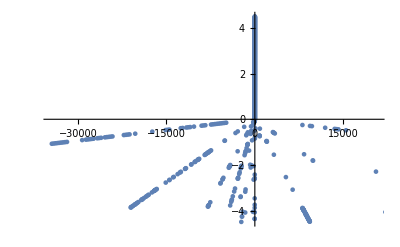

```mathematica
ListPlot[-{#[[2]],#[[1]]}&/@maalsadata]
```

```mathematica
ListPlot[-{#[[2]],#[[1]]}&/@maalsadata,PlotRange->{{-5,5},Automatic}]
```

-Graphics-

```mathematica
Show[
Graphics[
{Point[-{#[[2]],#[[1]]}&/@maalsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@maalsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@maalsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MAA",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
],FrameLabel->{"omega","k"}
]
```

Show::gtype: Symbol is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,Show[pltSpectGrids],FrameLabel→{omega,k}]

```mathematica
mzaplsadataClean
```

{{-2.191,-4.48891,-4.56117},{-2.091,-4.36108,4.63206},{-1.991,-4.23356,4.70304},{-1.891,-4.10637,4.77405},{-0.191,-1.94626,5.88681},{-0.091,-1.81083,5.94072}}

```mathematica
Part[mzaplsadata,
Flatten@Position[
Chop[
SpectrumOmegaKMZApEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@mzaplsadata),
10^(-5)
]//Quiet,
{0,0}]
]
```

{{-4.491,{-7.45476,3.03645}},{-4.391,{-7.32691,3.09766}},{-4.291,{-7.19882,3.1593}},{-4.191,{-7.07051,3.2214}},{-4.091,{-6.942,3.28396}},{-3.991,{-6.81329,3.34698}},{-3.891,{-6.68441,3.41047}},{-3.791,{-6.55536,3.47445}},{-3.691,{-6.42618,-3.53892}},{-3.591,{-6.29688,-3.60387}},{-3.491,{-6.16748,3.66932}},{-3.391,{-6.038,3.73527}},{-3.291,{-5.90848,3.8017}},{-3.191,{-5.77894,3.86863}},{-3.091,{-5.64941,3.93603}},{-2.991,{-5.51992,-4.0039}},{-2.891,{-5.39049,-4.07224}},{-2.791,{-5.26115,-4.141}},{-2.691,{-5.13195,4.21019}},{-2.591,{-5.0029,4.27976}},{-2.491,{-4.87405,4.34968}},{-2.291,{-4.61702,4.49044}},{-2.191,{-4.48891,-4.56117}},{-2.091,{-4.36108,4.63206}},{-1.991,{-4.23356,4.70304}},{-1.891,{-4.10637,4.77405}},{-1.791,{5.25663,-0.00149283}},{-1.691,{5.24782,-0.00189217}},{-1.591,{5.14811,0.00126675}},{-1.491,{5.23793,-0.00146836}},{-1.391,{5.10454,0.00194259}},{-1.291,{6.95804,0.00360852}},{-1.091,{5.84738,-0.00304775}},{-0.991,{5.55961,0.00355838}},{-0.891,{5.38593,-0.00375982}},{-0.791,{5.38126,0.00430323}},{-0.691,{6.20819,0.00632075}},{-0.591,{5.96773,0.00681494}},{-0.491,{5.52272,-0.00662215}},{-0.391,{5.67787,0.00989377}},{-0.291,{6.70021,-0.0115407}},{-0.191,{-1.94626,5.88681}},{-0.091,{-1.81083,5.94072}}}

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzaplsadataClean,VertexColors->colorf/@Rescale@(Abs[#[[3]]]&/@mzaplsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@mzaplsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-

```mathematica
mzamlsadataClean
```

{}

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzamlsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@mzamlsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@mzamlsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA-",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-

## Absolute Value of Log Argument

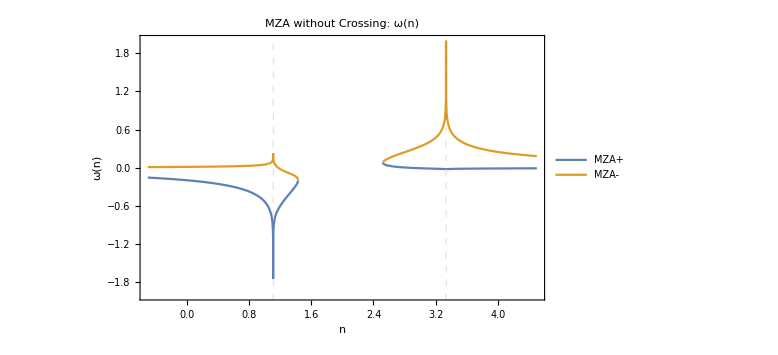

```mathematica
Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]]},{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{Automatic,{-2,2}},PlotLabel->"MZA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3},PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}]]
```

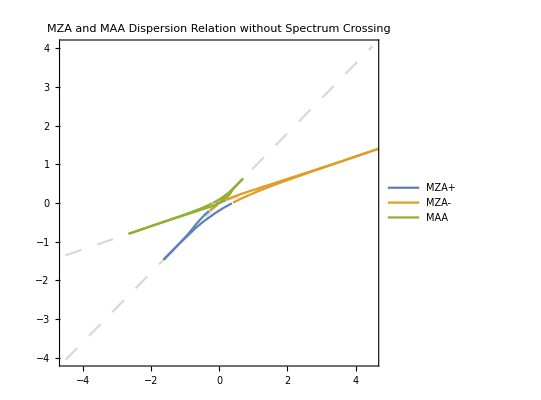

```mathematica
Show[
Plot[{0.3x,0.9x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]]},
{n ConAxialSymOmegaNMAAABS[n,{{{0.9,0.3},1}}],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.3},1}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

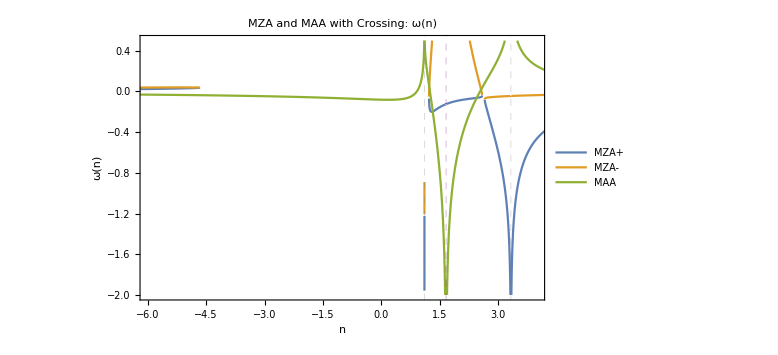

```mathematica
Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

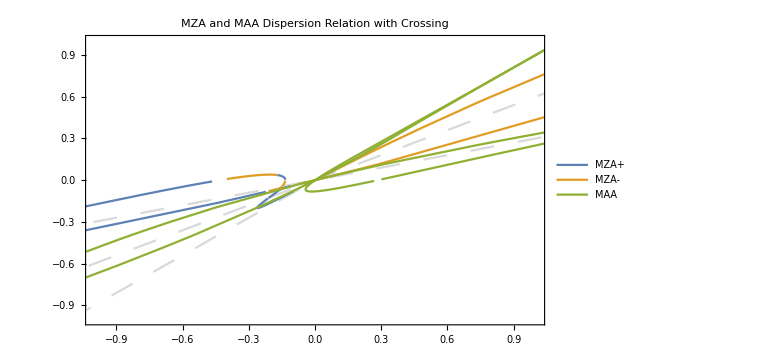

```mathematica
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,1}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

]
```

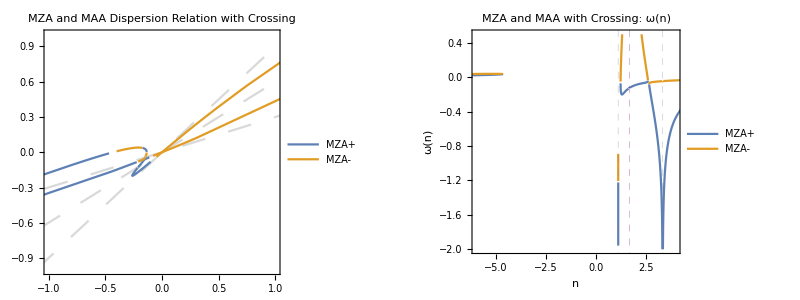

```mathematica
{{Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,1}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

],

Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
}}//Grid
```